```mathematica
f[t_,y_]:=3y^(2/3);
k1[h_]:=f[t,y];
k2[h_]:=f[t-0.5*h,y-0.5*h*k1[h]];
k3[h_]:=f[t-0.5*h,y-0.5*h*k2[h]];
k4[h_]:=f[t,y-h*k3[h]];
```

```mathematica
t0 = 0; y0 = 1;tm = 1;
```

```mathematica
m = 40;
```

```mathematica
h = (tm-t0)/m;
```

```mathematica
U=Array[u,{2,m+1},{0,0}];
u[0,0]=t0;u[1,0]=y0;
```

```mathematica
t=t0;y=y0;
Do[dy=h*(k1[h]+2*k2[h]+2*k3[h]+k4[h])/6;t=t+h;y=y+dy;u[0,i]=t;u[1,i]=y;
eps = u[1,i] - u[1, i-1];
Print["u[0,", i,"] = ", t, "     y"," = ", y, " eps = ", eps],{i,1,m}];
```

u[0,1] = 1/40     y = 1.07314 eps = 0.0731406

u[0,2] = 1/20     y = 1.14985 eps = 0.0767098

u[0,3] = 3/40     y = 1.23022 eps = 0.0803682

u[0,4] = 1/10     y = 1.31433 eps = 0.0841157

u[0,5] = 1/8     y = 1.40229 eps = 0.0879526

u[0,6] = 3/20     y = 1.49417 eps = 0.091879

u[0,7] = 7/40     y = 1.59006 eps = 0.0958949

u[0,8] = 1/5     y = 1.69006 eps = 0.1

u[0,9] = 9/40     y = 1.79426 eps = 0.104196

u[0,10] = 1/4     y = 1.90274 eps = 0.108481

u[0,11] = 11/40     y = 2.01559 eps = 0.112855

u[0,12] = 3/10     y = 2.13291 eps = 0.11732

u[0,13] = 13/40     y = 2.25479 eps = 0.121875

u[0,14] = 7/20     y = 2.38131 eps = 0.12652

u[0,15] = 3/8     y = 2.51256 eps = 0.131255

u[0,16] = 2/5     y = 2.64864 eps = 0.13608

u[0,17] = 17/40     y = 2.78964 eps = 0.140996

u[0,18] = 9/20     y = 2.93564 eps = 0.146002

u[0,19] = 19/40     y = 3.08674 eps = 0.151098

u[0,20] = 1/2     y = 3.24302 eps = 0.156285

u[0,21] = 21/40     y = 3.40458 eps = 0.161562

u[0,22] = 11/20     y = 3.57151 eps = 0.16693

u[0,23] = 23/40     y = 3.7439 eps = 0.172388

u[0,24] = 3/5     y = 3.92184 eps = 0.177937

u[0,25] = 5/8     y = 4.10542 eps = 0.183577

u[0,26] = 13/20     y = 4.29472 eps = 0.189307

u[0,27] = 27/40     y = 4.48985 eps = 0.195129

u[0,28] = 7/10     y = 4.69089 eps = 0.201041

u[0,29] = 29/40     y = 4.89794 eps = 0.207044

u[0,30] = 3/4     y = 5.11108 eps = 0.213138

u[0,31] = 31/40     y = 5.3304 eps = 0.219323

u[0,32] = 4/5     y = 5.556 eps = 0.225599

u[0,33] = 33/40     y = 5.78796 eps = 0.231966

u[0,34] = 17/20     y = 6.02639 eps = 0.238424

u[0,35] = 7/8     y = 6.27136 eps = 0.244974

u[0,36] = 9/10     y = 6.52298 eps = 0.251614

u[0,37] = 37/40     y = 6.78132 eps = 0.258346

u[0,38] = 19/20     y = 7.04649 eps = 0.265169

u[0,39] = 39/40     y = 7.31857 eps = 0.272083

u[0,40] = 1     y = 7.59766 eps = 0.279088

```mathematica
k1[h_]:=f[t,y];
k2[h_]:=f[t+0.25*h,y+0.25*h*k1[h]];
k3[h_]:=f[t+(3/8)*h,y+(3/32)*h*k1[h]+(9/32)*h*k2[h]];
k4[h_]:=f[t+(12/13)*h,y+h*((1932/2197)*k1[h]-(7200/2197)*k2[h]+(7296/2197)*k3[h])];
k5[h_]:=f[t+h,y+h*((439/216)*k1[h]-8*k2[h]+(3680/513)*k3[h]-(845/4104)*k4[h])];k6[h_]:=f[t+0.5*h,y+h*((8/27)*k1[h]+2*k2[h]+(3544/2565)*k3[h]-(1859/4104)*k4[h]-(11/40)*k5[h])];
m=20;t0=0;y0=1;tm=1;h=0.3;
t=t0;y=y0;
U=Array[u,{3,m+1},{0,0}];
u[0,0]=t0;u[1,0]=y0;u[2,0]=0;
Do[dy=h*((25/216)*k1[h]+(1408/2565)*k3[h]+(2197/4104)*k4[h]-(1/5)*k5[h]);
t=t+h;y=y+dy;
u[0,i]=t;u[1,i]=y;
epsilon=h*(k1[h]/360-(128/4275)*k3[h]-(2197/75240)*k4[h]+k5[h]/50+(2/5)*k6[h]);
u[2,i]=epsilon;Print["u[0,", i,"] = ", t, "     y"," = ", y, " eps = ", epsilon],{i,1,m}];
```

u[0,1] = 0.3     y = 2.19702 eps = 1.23008

u[0,2] = 0.6     y = 4.09607 eps = 1.69293

u[0,3] = 0.9     y = 6.85912 eps = 2.21653

u[0,4] = 1.2     y = 10.6482 eps = 2.80042

u[0,5] = 1.5     y = 15.6253 eps = 3.44427

u[0,6] = 1.8     y = 21.9523 eps = 4.14786

u[0,7] = 2.1     y = 29.7914 eps = 4.91102

u[0,8] = 2.4     y = 39.3045 eps = 5.73363

u[0,9] = 2.7     y = 50.6536 eps = 6.61559

u[0,10] = 3.     y = 64.0008 eps = 7.55683

u[0,11] = 3.3     y = 79.5079 eps = 8.55729

u[0,12] = 3.6     y = 97.337 eps = 9.61692

u[0,13] = 3.9     y = 117.65 eps = 10.7357

u[0,14] = 4.2     y = 140.609 eps = 11.9136

u[0,15] = 4.5     y = 166.376 eps = 13.1505

u[0,16] = 4.8     y = 195.114 eps = 14.4465

u[0,17] = 5.1     y = 226.983 eps = 15.8016

u[0,18] = 5.4     y = 262.146 eps = 17.2157

u[0,19] = 5.7     y = 300.765 eps = 18.6887

u[0,20] = 6.     y = 343.002 eps = 20.2208

```mathematica
Clear[y]
```

```mathematica
D[f[0,y],y]
```

2/y^(1/3)

```mathematica
2.7853/2
```

1.39265

```mathematica
Clear[t]
```

```mathematica
Clear[y]
```

```mathematica
Y =NDSolve[{y'[t]==3y[t]^(2/3), y[0]==1}, y,{t, 0, 1}, Method->"ExplicitRungeKutta"]
```

{{y→InterpolatingFunction[…]}}

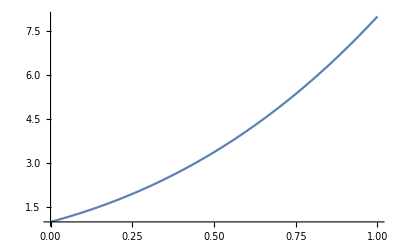

```mathematica
Plot[Evaluate[y[x]/.Y], {x, 0, 1}]
```